```mathematica
SetDirectory["D:\\newLight3"]
```

D:\newLight3

```mathematica
"D:\\newLight3"
```

D:\newLight3

```mathematica
(*cellColours={RGBColor[0.462745, 0.862745, 0.482353],RGBColor[0.37, 0.21, 0.],RGBColor[0.21, 0.21, 0.21],RGBColor[0., 0.73, 0.8200000000000001],RGBColor[1., 0.91, 0.04],RGBColor[0., 0.3, 0.8200000000000001],RGBColor[0.86, 0.74, 0.],RGBColor[0.98, 0.5700000000000001, 1.]};*)
cellColours={RGBColor[0.32, 0.6900000000000001, 0.],RGBColor[0.59, 0.32, 0.],RGBColor[0.21, 0.21, 0.21],RGBColor[0., 0.73, 0.8200000000000001],RGBColor[1., 0.93, 0.67],RGBColor[0., 0.5, 0.8200000000000001],RGBColor[0.92, 0.67, 0.],RGBColor[0.98, 0.81, 0.88]};
```

```mathematica
GetOrgCells[ org_,frameNo_]:=Module[{path,file,headings,applyHeading,items},
path = StringForm["output\\frame``.csv",frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Select[items,("o"/.#)==org&]
]
```

Use genome file to find out step of birth and (if dead) death, show frame in between (rounded to nearest saved)

```mathematica
GetOrgCells[org_]:=Module[{sMin, sMax,o,s},
sMin = "step"/.GetOrganism[org];
sMax=Check["step"/.GetOrgDeath[org],1160000]//Quiet;
o={};
For[i=0,Length[o]==0,i++,
s = Round[(sMin+sMax)/2,10^i];
o=Check[GetOrgCells[org,s],{}]//Quiet;
If[s==0,s="Not found";Break[];] (* No frame with organism saved *)
];
{s,o}
]
```

Should no organisms be found, it would be better to search both beneath and above middle life.

```mathematica
VisualizeOrg[org_]:=Module[{},
Graphics3D[Riffle[
cellColours⟦#+1⟧&/@("ct"/.org),
Sphere[{"x","z","y"},"r"]/.org
], Boxed->False,ImagePadding->None]
]
```

```mathematica
GetOrganism[orgNo_]:=With[{path=StringForm["organisms\\org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GetOrgDeath[orgNo_]:=With[{path=StringForm["orgDeaths\\org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GetOrgInfo[orgNo_]:=Module[{visStep,org,birth,death},
{visStep,org}=GetOrgCells[orgNo];
birth=GetOrganism[orgNo];
death=GetOrgDeath[orgNo]//Quiet;
{
"vis"-> Check[VisualizeOrg[org],orgNotOnRecord],
"id"-> orgNo,
"birthStep"-> "step"/.birth,
"visStep"-> visStep,
"deathStep"->Check["step"/.death,"Still alive"],
"generation"-> (getAncestors[orgNo]//Length)
}
]
```

```mathematica
VisualizeOrg[GetOrgCells[629146,1160000]]
```

-Graphics3D-

```mathematica
GetOrgInfo[0]//InfoCard2
```

-Graphics3D-
ID | 0
Birth | 0
Viewed | 10000
Death | 20003
Gen# | 1

```mathematica
ancestors=InfoCard[GetOrgInfo[#]]&/@(Downsample[getAncestors[630807],10])
```

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Riffle::list: List expected at position 1 in Riffle[ct,Sphere[{x,z,y},r]].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

{-Graphics3D- | ID | 630807
Birth | 1148044
Viewed | 1150000
Death | Still alive
Gen# | 255,-Graphics3D- | ID | 619086
Birth | 1114385
Viewed | 1120000
Death | 1134388
Gen# | 245,-Graphics3D- | ID | 599518
Birth | 1062417
Viewed | 1070000
Death | 1081924
Gen# | 235,-Graphics3D- | ID | 574454
Birth | 1000565
Viewed | 1010570
Death | 1020568
Gen# | 225,-Graphics3D- | ID | 564057
Birth | 976829
Viewed | 980000
Death | 981719
Gen# | 215,-Graphics3D- | ID | 549799
Birth | 945779
Viewed | 950000
Death | 953977
Gen# | 205,-Graphics3D- | ID | 530899
Birth | 906937
Viewed | 910000
Death | 915171
Gen# | 195,-Graphics- | ID | 525608
Birth | 896506
Viewed | Not found
Death | 897101
Gen# | 185,-Graphics3D- | ID | 518906
Birth | 883061
Viewed | 890000
Death | 890899
Gen# | 175,-Graphics- | ID | 502324
Birth | 851439
Viewed | Not found
Death | 854521
Gen# | 165,-Graphics- | ID | 497063
Birth | 841635
Viewed | Not found
Death | 846674
Gen# | 155,-Graphics3D- | ID | 477999
Birth | 806744
Viewed | 810000
Death | 821286
Gen# | 145,-Graphics3D- | ID | 463611
Birth | 780228
Viewed | 790000
Death | 790184
Gen# | 135,-Graphics- | ID | 451195
Birth | 758040
Viewed | Not found
Death | 758991
Gen# | 125,-Graphics3D- | ID | 427940
Birth | 717113
Viewed | 720000
Death | 720112
Gen# | 115,-Graphics3D- | ID | 399500
Birth | 667764
Viewed | 670000
Death | 671470
Gen# | 105,-Graphics- | ID | 385733
Birth | 644882
Viewed | Not found
Death | 646779
Gen# | 95,-Graphics- | ID | 352003
Birth | 590776
Viewed | Not found
Death | 592164
Gen# | 85,-Graphics3D- | ID | 316801
Birth | 536988
Viewed | 546990
Death | 556991
Gen# | 75,-Graphics3D- | ID | 290844
Birth | 501735
Viewed | 503440
Death | 505150
Gen# | 65,-Graphics- | ID | 259627
Birth | 465895
Viewed | Not found
Death | 468053
Gen# | 55,-Graphics3D- | ID | 181085
Birth | 384291
Viewed | 390000
Death | 404295
Gen# | 45,-Graphics3D- | ID | 117163
Birth | 324556
Viewed | 330000
Death | 332590
Gen# | 35,-Graphics3D- | ID | 35724
Birth | 245262
Viewed | 260000
Death | 265265
Gen# | 25,-Graphics3D- | ID | 5409
Birth | 136283
Viewed | 150000
Death | 154503
Gen# | 15,-Graphics3D- | ID | 238
Birth | 35226
Viewed | 45230
Death | 55229
Gen# | 5}

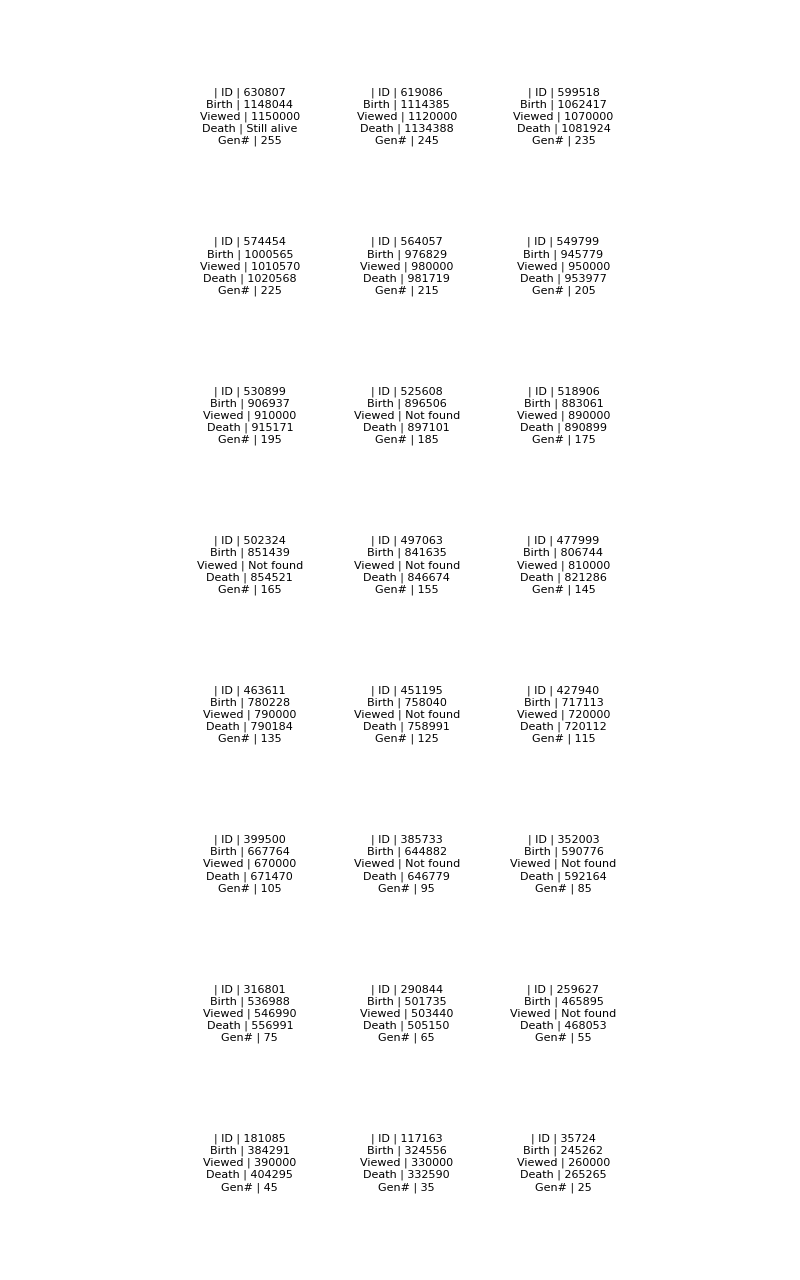

```mathematica
GraphicsGrid[Partition[ancestors,3],ImageSize->800,AspectRatio->1.6]
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\predLineage.png",%45,"PNG",ImageResolution->500]
```

C:\Users\admin\Documents\Joakim\repo\grafiliv\doc\figs\predLineage.png

```mathematica
getAncestors[org_]:=NestWhileList["parent"/.GetOrganism[#]&,org,#>0&];
```

```mathematica
RelationsGraph[orgs_]:=Module[{os,o1,o2,lca},
If[Length[orgs]<2,Return[Graph[orgs,{}]]];
os=Sort[orgs,Greater];
{o1,o2}=Take[os,2];
lca=GetLCA[o1,o2];
GraphUnion[
{lca-> o1,lca-> o2},
RelationsGraph[Append[Drop[os,2],lca]],
VertexLabels->"Name"
]
];
```

```mathematica
GetLCA[list_]:=GetLCA@@list;
```

```mathematica
RelationsGraph2[orgs_]:=Module[{os,o1,o2,lca},
If[Length[orgs]<2,Return[Graph[orgs,{}]]];
os=Sort[orgs,Greater];
o1=First[os];
os=Rest[os];
o2=MaximalBy[os,GetLCA[o1,#]&]//First;
lca=GetLCA[o1,o2];
GraphUnion[
If[lca≠o1,{lca-> o1},Graph[{}]],
If[lca≠o2,{lca-> o2},Graph[{}]],
RelationsGraph[Append[Complement[orgs,{o1,o2}],lca]],
VertexLabels->"Name"
]
];
```

```mathematica
RelationsGraph3Helper[orgs_]:=Module[{os,lcas,relations},
If[Length[orgs]<2,Return[Graph[orgs,{}]]];
os=Tuples[orgs,2];
lcas=ParallelMap[GetLCA,os];
relations = Table[{
lcas⟦i⟧-> First[os⟦i⟧],
lcas⟦i⟧-> Last[os⟦i⟧]},
{i,Length[os]}
]//Flatten//DeleteDuplicates;
relations=DeleteCases[relations,HoldPattern[x_->x_]];
Graph[
relations,VertexLabels->"Name"
]
];
```

```mathematica
RelationsGraph3[orgs_]:=With[
{g=FixedPoint[
RelationsGraph3Helper[VertexList[#]]&,
RelationsGraph3Helper[orgs]
]
},Graph[
(MaximalBy[#,First]//First)&/@GatherBy[EdgeList[g],Last],
VertexLabels->"Name"
]
]
```

```mathematica
VisualizeAllAncestors[org_]:=ParallelMap[InfoCard[GetOrgInfo[#]]&,getAncestors[org]];
```

```mathematica
GetLCA[o1_,o2_]:=Module[{a1,a2},
a1=o1;a2=o2;
While[a1≠a2,If[a1>a2,
a1="parent"/.GetOrganism[a1],
a2="parent"/.GetOrganism[a2]
]];
a1
];
```

```mathematica
GetLCA[574174,628131]
```

423464

```mathematica
GetLivingOrganisms[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["output\\frame``.csv",frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
```

```mathematica
orgNotOnRecord=Import["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\orgNotOnRecord.png"];
```

```mathematica
InfoCard[vis_]:=TableForm[{{"vis"/.vis, {{"ID", "id"/.vis}, {"Birth", "birthStep"/.vis}, {"Viewed", "visStep"/.vis}, {"Death", "deathStep"/.vis}, {"Gen#", "generation"/.vis}}}},TableSpacing->{0, 0}]
```

```mathematica
InfoCard2[vis_]:=TableForm[{{"vis"/.vis}, {{{"ID", "id"/.vis}, {"Birth", "birthStep"/.vis}, {"Viewed", "visStep"/.vis}, {"Death", "deathStep"/.vis}, {"Gen#", "generation"/.vis}}}},TableSpacing->{0, 0},TableAlignments->Center,TableSpacing->{0, 0}]
```

```mathematica
InfoTree[orgs_]:=Module[{tree,root,nodes},
tree=RelationsGraph3[orgs];
nodes=VertexList[tree];
root=Ordering[nodes,1]//First;
TreePlot[tree,Automatic,
root,
VertexRenderingFunction-> (Inset[InfoCard2[GetOrgInfo[nodes⟦#2⟧]],#1]&),
ImageSize->Full,VertexLabeling->True
]
];
```

```mathematica
living= GetLivingOrganisms[1160000];
Length[living]
```

4501

```mathematica
If[634960≠{634099,630807},{lca$5178905->o2$5178905},Graph[{}]]
```

If[634960≠{634099,630807},{lca$5178905→o2$5178905},Graph[{}]]

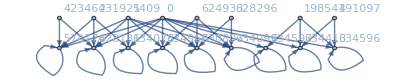

```mathematica
RelationsGraph3[{634078,574174,628131,634597,634413,634596,630807,634099,634960}]
```

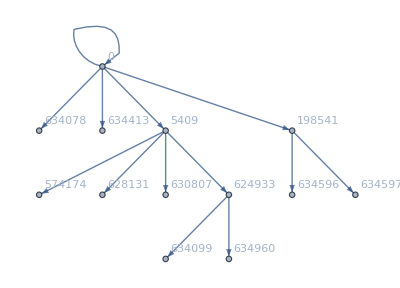

```mathematica
RelationsGraph2[{634078,574174,628131,634597,634413,634596,630807,634099,634960}]
```

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[ct,Sphere[{x,z,y},r]].

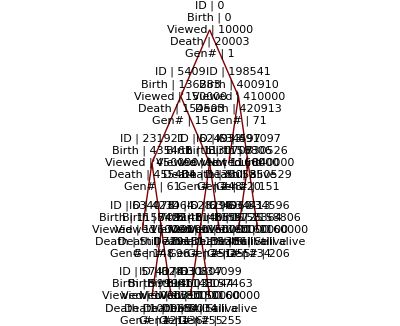

```mathematica
InfoTree[{634078,574174,628131,634597,634413,634596,630807,634099,634960}]
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\familyTree.PNG",%315,"PNG",ImageSize->1300,ImageResolution->1000]
```

C:\Users\admin\Documents\Joakim\repo\grafiliv\doc\figs\familyTree.PNG

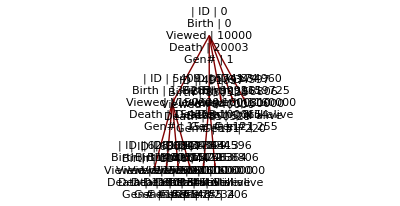

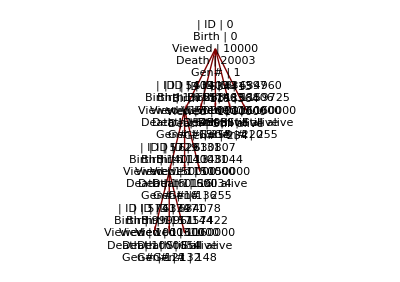

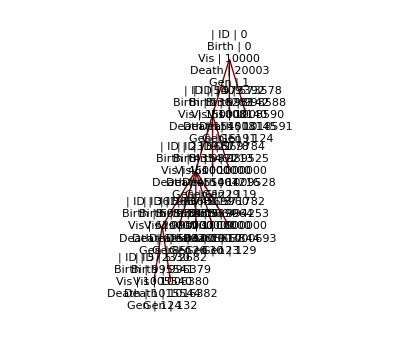

```mathematica
VisualizeAllAncestors[10]//Row
```

Import::nffil: File not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
VisualizeAllAncestors[435213]
```